```mathematica
a[n_]:= N[Cos[2/n]]
a[1]

Table[a[n], ]
```

-0.416147

Table::nliter: Non-list iterator Null at position 2 does not evaluate to a real numeric value.

Table[a[n],Null]

```mathematica
a[1]
```

Table::nliter: Non-list iterator Null at position 2 does not evaluate to a real numeric value.

```mathematica
Table[a[n], {n, 1, 30}]
```

{-0.416147,0.540302,0.785887,0.877583,0.921061,0.944957,0.959461,0.968912,0.97541,0.980067,0.983517,0.986143,0.988189,0.989813,0.991124,0.992198,0.993088,0.993834,0.994465,0.995004,0.995468,0.995871,0.996222,0.99653,0.996802,0.997043,0.997258,0.99745,0.997623,0.997779}

```mathematica
TableForm[Table[{n, a[n]}, {n,1,30}]]
```

1 | -0.416147
2 | 0.540302
3 | 0.785887
4 | 0.877583
5 | 0.921061
6 | 0.944957
7 | 0.959461
8 | 0.968912
9 | 0.97541
10 | 0.980067
11 | 0.983517
12 | 0.986143
13 | 0.988189
14 | 0.989813
15 | 0.991124
16 | 0.992198
17 | 0.993088
18 | 0.993834
19 | 0.994465
20 | 0.995004
21 | 0.995468
22 | 0.995871
23 | 0.996222
24 | 0.99653
25 | 0.996802
26 | 0.997043
27 | 0.997258
28 | 0.99745
29 | 0.997623
30 | 0.997779

```mathematica
Plot the first 50 terms of the above sequence.
ListPlot[Table[{n, a[n]}, {n,1,50}]]
```

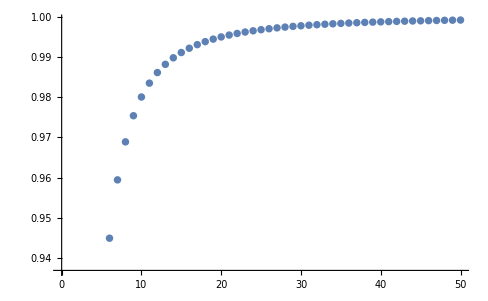
```mathematica
50 above first of Plot terms the^2 sequence.-Graphics-
Manipulate[ListPlot[Table[{n, a[n]}, {n,1,k}]], {k, 1, 100}]
```

50 above first of Plot terms the^2 sequence.-Graphics-

```mathematica
Limit[a[n], {n-> Infinity}]
```

1.

```mathematica
0 0
1 1
2 2
3 4
4 7
5 12
6 20
7 29
8 38
9 52
10 73
11 94
12 127
13 151
14 181
15 211
16 257
17 315
18 373
19 412
20 475
21 530
22 545
23 607
24 716
25 797
26 861
27 964
28 1059
```

0

1

4

12

28

60

120

203

304

468

730

1034

1524

1963

2534

3165

4112

5355

6714

7828

9500

11130

11990

13961

17184

19925

22386

26028

29652

```mathematica
List, Arrays and Matrics
```

```mathematica
{1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
%^2
```

{1,4,9,16,25}

```mathematica
a = {1,2,3,4,5}
```

{1,2,3,4,5}

```mathematica
a^2
```

{1,4,9,16,25}

```mathematica
First[a]
```

1

```mathematica
Last[a]
```

5

```mathematica
Take[a,{2,4,2}]
```

{2,4}

```mathematica
Drop[a,{2,4,2}]
```

{1,3,5}

```mathematica
a[[3]]
```

3

```mathematica
Range[50]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
Range[-3,10,2]
```

{-3,-1,1,3,5,7,9}

```mathematica
S = {{0,0},{1,1},{2,2},{3,4},{4,7},{5,12},{6,20},{7,29},{8,38},{9,52},{10,73},{11,94},{12,127},{13,151},{14,181},{15,211},{16,257},{17,315},{18,373},{19,412},{20,475}}
```

{{0,0},{1,1},{2,2},{3,4},{4,7},{5,12},{6,20},{7,29},{8,38},{9,52},{10,73},{11,94},{12,127},{13,151},{14,181},{15,211},{16,257},{17,315},{18,373},{19,412},{20,475}}

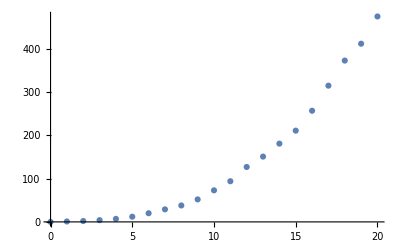

```mathematica
ListPlot[S, PlotMarkers->Automatic]
```

```mathematica
TableForm[S, TableHeadings->{{"Sequence"}, {{"nth tern"}, "Value of the Sequence"}} ]
```

| {nth tern} | Value of the Sequence
Sequence | 0 | 0
 | 1 | 1
 | 2 | 2
 | 3 | 4
 | 4 | 7
 | 5 | 12
 | 6 | 20
 | 7 | 29
 | 8 | 38
 | 9 | 52
 | 10 | 73
 | 11 | 94
 | 12 | 127
 | 13 | 151
 | 14 | 181
 | 15 | 211
 | 16 | 257
 | 17 | 315
 | 18 | 373
 | 19 | 412
 | 20 | 475

```mathematica
ListPlot[{{0,0},{1,1},{2,2},{3,4},{4,7},{5,12},{6,20},{7,29},{8,38},{9,52},{10,73},{11,94},{12,127},{13,151},{14,181},{15,211},{16,257},{17,315},{18,373},{19,412},{20,475}}, {n,1,20}]
```

ListPlot::nonopt: Options expected (instead of {n,1,20}) beyond position 1 in ListPlot[{{0,0},{1,1},{2,2},{3,4},{4,7},{5,12},{6,20},{7,29},{8,38},{9,52},«11»},{n,1,20}]. An option must be a rule or a list of rules.

ListPlot[{{0,0},{1,1},{2,2},{3,4},{4,7},{5,12},{6,20},{7,29},{8,38},{9,52},{10,73},{11,94},{12,127},{13,151},{14,181},{15,211},{16,257},{17,315},{18,373},{19,412},{20,475}},{n,1,20}]